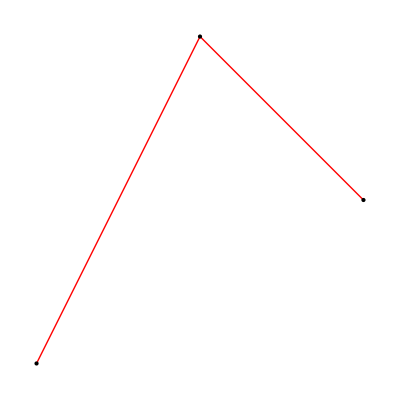

-Graphics3D-

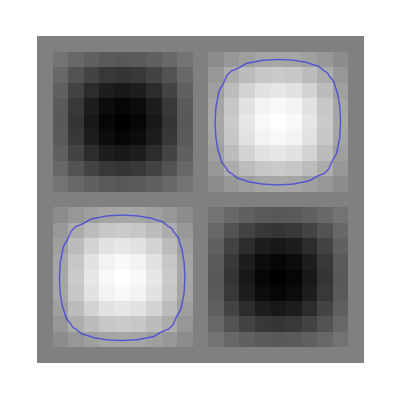

```mathematica
mypoly={{{0,0},{1,2},{2,1}},{{1,2},{2,3}}};
mymesh={{{0,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,2,3},{1,2,4}}};SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
showGrayImage[img_]:=Graphics[Raster[Transpose[(img-Min[img])/(Max[img]-Min[img])],{{.5,.5},Dimensions[img]+.5}],Frame->False];
showCurve[{V_,E_},col_]:=Graphics[{{col,Map[Line[V⟦#⟧]&,E]},Map[Point,V]},Frame->False];
showCurveNoPoints[{V_,E_},col_]:=Graphics[{col,Map[Line[V⟦#⟧]&,E]},Frame->False];
showSurface[{V_,T_},col_]:=Graphics3D[{col,Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral"];

showCurve[mypoly,RGBColor[1,0,0]]
showSurface[mymesh,RGBColor[1,0,0]]

showSurfaceNoEdges[{V_,T_},col_]:=Graphics3D[{col,EdgeForm[{}],Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral"];
showMathematica[img_,iso_]:=ListContourPlot[Transpose[img],Contours->{iso},ContourShading->None,ContourStyle->RGBColor[0,0,1],Frame->False,DataRange->Transpose[{{1,1},Dimensions[img]}]];
showMathematica3D[img_,iso_]:=ListContourPlot3D[Transpose[img,{3,2,1}],Contours->{iso},ContourStyle->{RGBColor[.5,.5,1]},DataRange->Transpose[{{1,1,1},Dimensions[img]}],Axes->False,RotationAction->Clip,Lighting->"Neutral",PlotRange->All,BoxRatios->Automatic];
volSyn=Table[N[Sin[x]Sin[y]Sin[z]],{x,0,2π,2π/10},{y,0,2π,2π/10},{z,0,2π,2π/10}];
imgSyn=Table[N[Sin[x]Sin[y]],{x,0,2π,2π/20},{y,0,2π,2π/20}];
imgCryo=GIFtoGray["cryo.gif"];
cycles=Get["cycles.txt"];
Show[showGrayImage[imgSyn],showMathematica[imgSyn,.3]]
```

```mathematica
Dimensions[imgSyn]
```

{21,21}

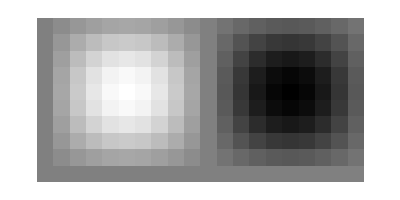

```mathematica
showGrayImage[imgSyn[[1;;20,1;;10]]]
```